```mathematica
(* This notebook solves and simulates the PerfForesightCRRA-RandSav model *)
```

Solving ...

Below 𝓂MinPermitted after 279 backwards Euler iterations.

Last 2 Points:(1.63897 | 0.517385 | 0.189731 | -22.5245 | -0.0845471
0.977083 | 0.367608 | 0.273336 | -25.9326 | -0.179373)

Solving ...

Above 𝓂MaxPermitted after 439 backwards Euler iterations.

Last 2 Points:(99.4607 | 6.62572 | 0.0568245 | -2.66862 | -7.57009×10^-6
100.607 | 6.69085 | 0.0568159 | -2.64277 | -7.3254×10^-6)

Solving ...

Below 𝓂MinPermitted after 177 backwards Euler iterations.

Last 2 Points:(1.01652 | 0.379804 | 0.269597 | -24.8988 | -0.17008
0.0292269 | 0.0133888 | 0.457804 | -185.949 | -0.0298347)

Solving ...

Above 𝓂MaxPermitted after 294 backwards Euler iterations.

Last 2 Points:(99.3607 | 6.70889 | 0.0570182 | -2.6326 | -0.0000108132
101.086 | 6.80723 | 0.057 | -2.59483 | -0.0000103166)

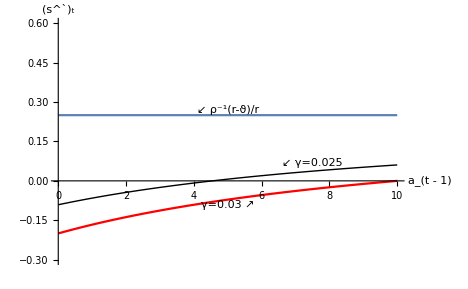

Exporting figure to ./Figures/savRatePFCompare.xxx

Null

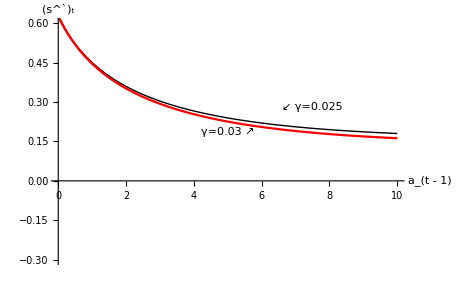

Exporting figure to ./Figures/savRateBufferStockCompare.xxx

Null

```mathematica
(* This cell is basically housekeeping and setup stuff; it can be ignored *)
ClearAll["Global`*"];ParamsAreSet=False;
If[Length[$FrontEnd] > 0,NBDir=SetDirectory[NotebookDirectory[]]];(* If running from the Notebook interface *)
If[$VersionNumber<9,(*then*) Print["These programs require Mathematica version 9 or greater."];Abort[]];
(* If running from shell, must start from inside same directory in which notebook resides *)
AutoLoadDir=SetDirectory["../../CoreCode/Autoload"];Get["./init.m"];
CoreCodeDir=SetDirectory[".."];
rootDir = SetDirectory[".."];
Get[CoreCodeDir<>"/MakeAnalyticalResults.m"];
Get[CoreCodeDir<>"/VarsAndFuncs.m"];
(* Method of creating figures depends on whether being run in batch mode or interactively *)
If[$FrontEnd == Null,OpenFigsUsingShell=True,OpenFigsUsingShell=False]; 
TractableFigDir=SetDirectory[rootDir<>"/Examples/PerfForesightCRRA-RandSav/Figures/"];
TractableCodeDir=SetDirectory[rootDir<>"/Examples/PerfForesightCRRA-RandSav"];

(* For the definition of the saving rate, see handout PerfForesightCRRA *)
income[atm1_]:= atm1 ((R)-1)+1;
savRateBufferStock[atm1_]:=(income[atm1]-cE[atm1 (R)+1])/income[atm1];
(* For the derivation of this expression, see handout PerfForesightCRRA *)
savRatePF[atm1_]:=((((1/ρ)((r)-ϑ))-𝔤)/((r)-𝔤)+(1/ρ)((r)-ϑ)atm1)/(1+(r)atm1);

Get[CoreCodeDir<>"/ParametersBase.m"];

{aMin,aMax}={0.,10};
{sMin,sMax}={-0.3,0.6};
r=0.08;ϑ=0.04;𝔤=0.025;FindStableArm;
savRateAtInfty=((1/ρ)((r)-ϑ))/(r);
savRateInftyPlot=Plot[savRateAtInfty
,{atm1,aMin,aMax}
,PlotStyle->{Dashed[{0.02}]}];
savRatePF0=Plot[savRatePF[atm1]
,{atm1,aMin,aMax}
,PlotRange->{Automatic,{sMin,sMax}}
];
savRateBufferStock0=Plot[savRateBufferStock[atm1],{atm1,aMin,aMax}];
𝔤=0.03;
FindStableArm;
savRatePF1=Plot[savRatePF[atm1],{atm1,aMin,aMax},PlotRange->{Automatic,{sMin,sMax}},PlotStyle->Red];
savRateBufferStock1=Plot[savRateBufferStock[atm1],{atm1,aMin,aMax}
,PlotStyle->Red
];
savRatePFCompare = Show[savRatePF0,savRatePF1,savRateInftyPlot
,Graphics[Text["↙ ρ^-1(r-ϑ)/r",{(aMax-aMin)/2,savRateAtInfty},{0,-1}]]
,Graphics[Text["↙ γ=0.025",{(aMax-aMin)(3/4),0.08+savRatePF[(aMax-aMin)(3/4)]},{0,-1}]]
,Graphics[Text["γ=0.03 ↗",{(aMax-aMin)/2,savRatePF[(aMax-aMin)/2]},{0,1}]]
,AxesLabel->{"a_(t - 1)","(s^`)_t"}
,PlotRange->{Automatic,{sMin,sMax}}
,AxesOrigin->{0.,0.}
];

ExportFigsToDir["savRatePFCompare","./Figures"];
savRateBufferStockCompare=Show[savRateBufferStock0,savRateBufferStock1
,Graphics[Text["↙ γ=0.025",{(aMax-aMin)(3/4),0.08+savRateBufferStock[(aMax-aMin)(3/4)]},{0,-1}]]
,Graphics[Text["γ=0.03 ↗",{(aMax-aMin)/2,-0.02+savRateBufferStock[(aMax-aMin)/2]},{0,1}]]
,AxesLabel->{"a_(t - 1)","(s^`)_t"}
,PlotRange->{Automatic,{sMin,sMax}}
,AxesOrigin->{0.,0.}];
ExportFigsToDir["savRateBufferStockCompare","./Figures"];
```